```mathematica
data=Rest[Import["/home/rhennigan/classes/Computing II/git/GOOG.csv"]]⟦All,7⟧
```

{539.78,543.98,532.71,526.54,520.84,511.17,524.51,530.03,537.94,533.21,544.49,560.88,572.5,563.74,577.35,575.28,570.08,568.27,577.36,576.36,577.1,575.06,587.99,581.13,587.37,596.08,589.27,584.77,579.95,573.1,575.62,581.35,583.1,581.01,589.72,586.08,581.98,577.94,577.33,571.6,569.2,571.,577.86,580.2,582.56,583.37,584.49,586.86,582.16,573.48,574.65,574.78,562.73,567.88,568.77,563.36,566.37,565.07,573.15,566.07,571.6,587.42,585.61,590.6,589.02,593.35,595.98,594.74,589.47,595.08,573.73,582.66,584.78,584.87,579.18,571.1,576.08,571.09,582.25,584.73,582.34,582.67,575.28,577.24,576.,578.65,564.62,564.95,556.36,554.9,553.37,543.01,544.28,551.76,551.35,558.84,560.55,562.12,556.33,553.9,544.66,544.94,553.93,559.89,560.08,561.68,565.95,552.7,545.06,538.94,529.77,528.86,520.63,519.98,526.65,533.09,529.92,518.73,511.,509.96,515.14,527.81,527.93,531.35,526.66,527.7,517.15,516.18,525.16,526.94,534.81,528.62,536.1,556.54,536.44,532.52,530.6,540.95,564.14,554.9,538.15,543.14,569.74,567.,567.16,556.97,559.99,558.46}

```mathematica
Length[data]
```

148

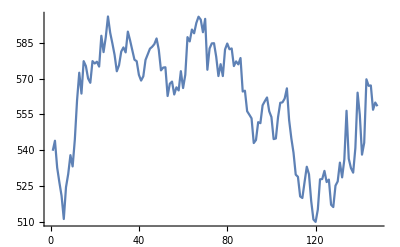

```mathematica
ListLinePlot[data]
```

```mathematica
GaussianMatrix[{{6},.75}]
```

{3.96129×10^-7,8.46664×10^-6,0.000150914,0.0021548,0.0231355,0.166674,0.615753,0.166674,0.0231355,0.0021548,0.000150914,8.46664×10^-6,3.96129×10^-7}

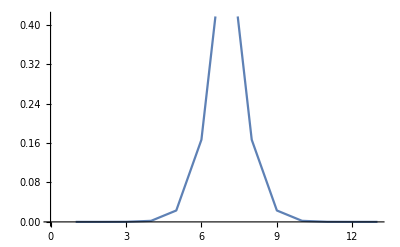

```mathematica
ListLinePlot[%]
```

```mathematica
σ=2;
g=Table[1/(√(2Pi)σ)ⅇ^(-x^2/(2 σ^2)),{x,-10,10}]
```

{1/(2 ⅇ^(25/2) √(2 π)),1/(2 ⅇ^(81/8) √(2 π)),1/(2 ⅇ^8 √(2 π)),1/(2 ⅇ^(49/8) √(2 π)),1/(2 ⅇ^(9/2) √(2 π)),1/(2 ⅇ^(25/8) √(2 π)),1/(2 ⅇ^2 √(2 π)),1/(2 ⅇ^(9/8) √(2 π)),1/(2 √(2 ⅇ π)),1/(2 ⅇ^(1/8) √(2 π)),1/(2 √(2 π)),1/(2 ⅇ^(1/8) √(2 π)),1/(2 √(2 ⅇ π)),1/(2 ⅇ^(9/8) √(2 π)),1/(2 ⅇ^2 √(2 π)),1/(2 ⅇ^(25/8) √(2 π)),1/(2 ⅇ^(9/2) √(2 π)),1/(2 ⅇ^(49/8) √(2 π)),1/(2 ⅇ^8 √(2 π)),1/(2 ⅇ^(81/8) √(2 π)),1/(2 ⅇ^(25/2) √(2 π))}

```mathematica
g=g/Total[g];
```

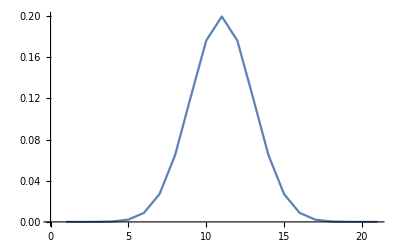

```mathematica
ListLinePlot[g,PlotRange->All]
```

```mathematica
N[Pi]
```

3.14159

```mathematica
N[g]
```

{7.4336×10^-7,7.99187×10^-6,0.0000669151,0.000436341,0.00221592,0.00876415,0.0269955,0.0647588,0.120985,0.176033,0.199471,0.176033,0.120985,0.0647588,0.0269955,0.00876415,0.00221592,0.000436341,0.0000669151,7.99187×10^-6,7.4336×10^-7}

```mathematica
smooth=ListConvolve[g,data];
```

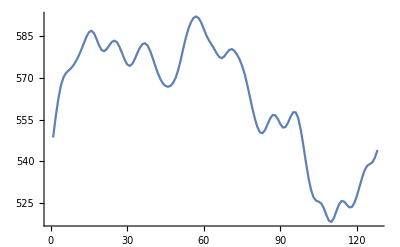

```mathematica
ListLinePlot[smooth]
```

```mathematica
Table[{i,i+j,FullSimplify[Total[g⟦i;;i+j⟧]]},{i,1,Length[g]},{j,0,Length[g]-i}]
```

```mathematica
day + day - i
```

2 day-i

```mathematica
smooth[[1;;25]]
```

{548.63,555.832,562.214,567.022,570.074,571.718,572.622,573.456,574.599,576.1,577.912,580.022,582.36,584.649,586.384,586.976,586.097,584.037,581.676,580.016,579.62,580.382,581.72,582.928,583.406}

```mathematica
files=Sort[FileNames["/home/rhennigan/Pictures/*"]]⟦-10;;⟧
```

{/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:04:35.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:04:39.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:04:49.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:04:54.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:05:22.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:05:31.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:05:42.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:05:49.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:06:11.png,/home/rhennigan/Pictures/Screenshot from 2014-10-26 00:06:20.png}

```mathematica
img=ImageAssemble[Partition[Import/@files,2]];
```

```mathematica
Export["/home/rhennigan/classes/Computing II/HW6/output.pdf",img]
```

/home/rhennigan/classes/Computing II/HW6/output.pdf

```mathematica
img=ImageAssemble[Partition[Import/@Sort[FileNames["/home/rhennigan/classes/Computing II/HW5/submit/misc/*.png"]],3]
];
Export["/home/rhennigan/classes/Computing II/HW5/submit/misc/output.pdf", img]
```

/home/rhennigan/classes/Computing II/HW5/submit/misc/output.pdf